# Parameter Robustness of the Traynard Logistic Cell-Cycle Network

## Latin-hypercube sweep over the 33-dimensional kinetic-parameter box

Ismail Belgacem, 2026.  Manuscript MBS-D-26-00594, Section 5.5 (Figure 5).  The regulatory functions are DERIVED from the Boolean rules by the same BooleanToLogisticODE toolkit used throughout the paper - the package BooleanToLogisticODE` (BooleanToLogisticODE.m), the function BooleanToOdeSystem (recursive De Morgan map), and the kernels logisticp / logisticm (activation / repression).  A Latin-hypercube sweep over the 33-dimensional kinetic-parameter box (kappa_i ~ U(50,100), gamma_i ~ U(0.25,2), theta_i ~ U(10,20)) is run with the proliferative initial condition (Table 2) held fixed.  Each sampled system is integrated over t in [0,100] and classified as a SUSTAINED LIMIT CYCLE when at least 3 of the 6 canonical species {Cdc20, Cdh1, CycA, CycB, E2F, UbcH10} retain relative oscillation amplitude above 5% on the late window t in [60,100].

The steepness sweep (n = 4, 8, 16) prints the sustained-cycle fractions and median periods, and the last section writes the figure traynard_robustness_mma.png.

## Setup

```mathematica
(* Setup: load the translation package, protect the ODE variable t, fix the seed *)
SetDirectory[NotebookDirectory[]];
Needs["BooleanToLogisticODE`"];
Unprotect[t]; Clear[t]; Protect[t];
SeedRandom[12345];
```

## Gene set

```mathematica
(* Gene set and the canonical oscillating subset *)
genes = {Cdc20, Cdh1, CycA, CycB, CycE, E2F, p27, Rb, Skp2, UbcH10, CycD};
cyc   = {Cdc20, Cdh1, CycA, CycB, E2F, UbcH10};   (* 6 canonical species *)
```

## Boolean network (minimal DNF)

```mathematica
(* Boolean network (identical to the R / Python driver), reduced to minimal DNF *)
FB = {
  Cdc20  -> CycB,
  Cdh1   -> (! CycA && ! CycB) || p27,
  CycA   -> (! Cdc20 && ! Cdh1 && CycA) || (! Cdc20 && ! Cdh1 && E2F && ! Rb) ||
            (CycA && ! UbcH10) || (E2F && ! Rb && ! UbcH10),
  CycB   -> (! Cdc20 && ! Cdh1) || (! Cdh1 && ! UbcH10),
  CycE   -> E2F && ! Rb,
  E2F    -> (! Cdc20 && ! CycA && ! Rb) || (! Cdc20 && p27 && ! Rb) ||
            (! CycA && ! CycB && ! Rb) || (! CycB && p27 && ! Rb),
  p27    -> (! CycA && ! CycB && ! CycD && ! CycE) || (! CycA && ! CycB && ! CycD && p27) ||
            (! CycB && ! CycD && ! CycE && p27) || (! CycD && ! Skp2),
  Rb     -> (! CycA && ! CycB && ! CycD && ! CycE) || (! CycA && ! CycD && p27) ||
            (! CycB && ! CycD && p27) || (! CycD && ! CycE && p27),
  Skp2   -> ! Cdh1 || ! Rb,
  UbcH10 -> (Cdc20 && UbcH10) || ! Cdh1 || (CycA && UbcH10) || (CycB && UbcH10),
  CycD   -> CycD
};

FBmin = FB /. (g_ -> f_) :> (g -> BooleanMinimize[f, "DNF"]);
```

## Initial condition and Table 2 baseline parameters

```mathematica
(* Proliferative initial condition (Table 2), held fixed *)
var0 = <|
  Cdc20 -> 0.54, Cdh1 -> 38.68, CycA -> 96.61, CycB -> 64.56, CycE -> 40.97,
  E2F -> 69.56, p27 -> 5.55, Rb -> 32.23, Skp2 -> 63.64, UbcH10 -> 45.80, CycD -> 58.36
|>;

(* Table 2 baseline kinetic parameters (for the overlaid realisation) *)
kappa0 = <| Cdc20 -> 74.33, Cdh1 -> 61.00, CycA -> 79.17, CycB -> 76.70, CycE -> 91.06,
            E2F -> 56.50, p27 -> 68.79, Rb -> 53.20, Skp2 -> 66.65, UbcH10 -> 73.51, CycD -> 64.75 |>;
gamma0 = <| Cdc20 -> 0.70, Cdh1 -> 1.45, CycA -> 1.74, CycB -> 0.94, CycE -> 0.58,
            E2F -> 0.58, p27 -> 0.68, Rb -> 1.24, Skp2 -> 0.43, UbcH10 -> 1.95, CycD -> 0.76 |>;
theta0 = <| Cdc20 -> 19.18, Cdh1 -> 11.84, CycA -> 19.29, CycB -> 18.84, CycE -> 18.90,
            E2F -> 17.30, p27 -> 14.69, Rb -> 11.73, Skp2 -> 12.95, UbcH10 -> 12.05, CycD -> 19.89 |>;
```

## Latin-hypercube sampler and integration

```mathematica
(* Latin-hypercube sampler: m points in the d-dimensional unit cube *)
latinHypercube[m_Integer, d_Integer] :=
  Transpose@Table[(RandomSample[Range[m]] - 1 + RandomReal[{0, 1}, m])/m, {d}];

(* Integrate one sampled system; return gene -> InterpolatingFunction *)
integrateSystem[kap_Association, gam_Association, th_Association, n_, tmax_ : 100] :=
  Module[{eqs, sol},
    eqs = BooleanToOdeSystem[FBmin, t, kap, gam, th, n, var0, {logisticm, logisticp}];
    sol = Quiet@Check[
        NDSolve[eqs, genes, {t, 0, tmax},
          Method -> "StiffnessSwitching", MaxSteps -> 10^6,
          PrecisionGoal -> 6, AccuracyGoal -> 6], $Failed];
    If[sol === $Failed || Head[sol] =!= List || sol === {}, $Failed,
       AssociationThread[genes -> (genes /. First[sol])]]
  ];
```

## Late-window amplitude, period, and limit-cycle classifier

```mathematica
(* Late-window amplitude and period (mid-level up-crossings) *)
lateAmpPeriod[f_, win_ : 60, tmax_ : 100, npts_ : 801] :=
  Module[{ts, ys, ymax, ymin, amp, mid, cross, per},
    ts   = Subdivide[win, tmax, npts - 1];
    ys   = f /@ ts;
    ymax = Max[ys]; ymin = Min[ys]; amp = ymax - ymin; mid = (ymax + ymin)/2;
    cross = Select[Range[Length[ys] - 1], ys[[#]] < mid && ys[[# + 1]] >= mid &];
    per  = If[Length[cross] >= 2, Mean[Differences[ts[[cross]]]], Missing[]];
    {amp, per}
  ];

(* Classify one solution as a sustained limit cycle *)
sustainedCycle[traj_Association, ceil_Association] :=
  Module[{count = 0, bestAmp = 0, bestPer = Missing[], ap, rel},
    Do[
      ap  = lateAmpPeriod[traj[g]];
      rel = ap[[1]]/ceil[g];
      If[NumericQ[rel] && rel > 0.05,
         count++;
         If[! MissingQ[ap[[2]]] && ap[[1]] > bestAmp, bestAmp = ap[[1]]; bestPer = ap[[2]]]
      ],
      {g, cyc}];
    {count >= 3 && ! MissingQ[bestPer], bestPer}
  ];
```

## Steepness sweep n = 4, 8, 16

```mathematica
(* One Latin-hypercube sweep at fixed steepness n *)
runSweep[n_, M_ : 400] :=
  Module[{U, lo, hi, osc = 0, ok = 0, periods = {}, v, kap, gam, th, traj, ceil, res},
    U  = latinHypercube[M, 33];
    lo = Join[ConstantArray[50., 11], ConstantArray[0.25, 11], ConstantArray[10., 11]];
    hi = Join[ConstantArray[100., 11], ConstantArray[2.0, 11], ConstantArray[20., 11]];
    Do[
      v   = lo + U[[m]] (hi - lo);
      kap = AssociationThread[genes -> v[[1 ;; 11]]];
      gam = AssociationThread[genes -> v[[12 ;; 22]]];
      th  = AssociationThread[genes -> v[[23 ;; 33]]];
      traj = integrateSystem[kap, gam, th, n];
      If[traj =!= $Failed,
        ok++;
        ceil = AssociationThread[genes -> (Values[kap]/Values[gam])];
        res  = sustainedCycle[traj, ceil];
        If[res[[1]], osc++; AppendTo[periods, res[[2]]]]
      ],
      {m, M}];
    <| "n" -> n, "M" -> M, "solverOK" -> ok, "osc" -> osc,
       "frac" -> 100. osc/M, "periods" -> periods,
       "periodMedian" -> If[periods === {}, Missing[], Median[periods]] |>
  ];

(* Run the steepness sweep n = 4, 8, 16 *)
results = Table[runSweep[n, 400], {n, {4, 8, 16}}];
Do[
  Print@StringForm[
    "n=`1` : solver OK `2`/`3`, sustained cycle `4`/`3` = `5`%, period median `6`",
    r["n"], r["solverOK"], r["M"], r["osc"], NumberForm[r["frac"], {4, 1}],
    If[MissingQ[r["periodMedian"]], "NA", NumberForm[r["periodMedian"], {5, 2}]]],
  {r, results}];
```

n=4 : solver OK 400/400, sustained cycle 62/400 = 15.5%, period median 83/15

n=8 : solver OK 400/400, sustained cycle 177/400 = 44.3%, period median 49/10

n=16 : solver OK 400/400, sustained cycle 243/400 = 60.8%, period median 101/20

## Figure (a): E2F trajectories across 60 draws

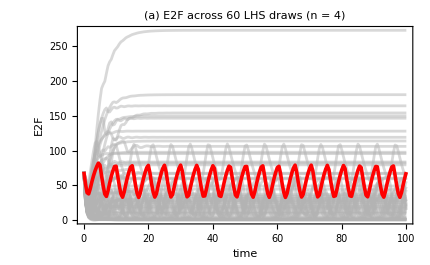

```mathematica
(* (a) E2F trajectories for 60 draws at n = 4, with the Table 2 realisation overlaid *)
nBatch = 60;
Ua  = latinHypercube[nBatch, 33];
loa = Join[ConstantArray[50., 11], ConstantArray[0.25, 11], ConstantArray[10., 11]];
hia = Join[ConstantArray[100., 11], ConstantArray[2.0, 11], ConstantArray[20., 11]];
e2fCurves = Table[
   Module[{v, kap, gam, th, traj},
     v   = loa + Ua[[m]] (hia - loa);
     kap = AssociationThread[genes -> v[[1 ;; 11]]];
     gam = AssociationThread[genes -> v[[12 ;; 22]]];
     th  = AssociationThread[genes -> v[[23 ;; 33]]];
     traj = integrateSystem[kap, gam, th, 4];
     If[traj === $Failed, Missing[], Table[{tt, traj[E2F][tt]}, {tt, 0, 100, 0.5}]]
   ], {m, nBatch}];
e2fCurves = DeleteMissing[e2fCurves];

(* Table 2 realisation (baseline) at n = 4, and its E2F period *)
trajBase = integrateSystem[kappa0, gamma0, theta0, 4];
e2fBase  = Table[{tt, trajBase[E2F][tt]}, {tt, 0, 100, 0.5}];
perBase  = lateAmpPeriod[trajBase[E2F]][[2]];   (* ~ 5.07 *)

panelA = Show[
   ListLinePlot[e2fCurves, PlotStyle -> Directive[GrayLevel[0.7], Opacity[0.5]]],
   ListLinePlot[{e2fBase}, PlotStyle -> Directive[Red, Thickness[0.006]]],
   Frame -> True, FrameLabel -> {"time", "E2F"},
   PlotLabel -> "(a) E2F across 60 LHS draws (n = 4)", PlotRange -> All, ImageSize -> 430]
```

## Figure (b): sustained-cycle fraction vs steepness, and export

figure written: traynard_robustness_mma.png

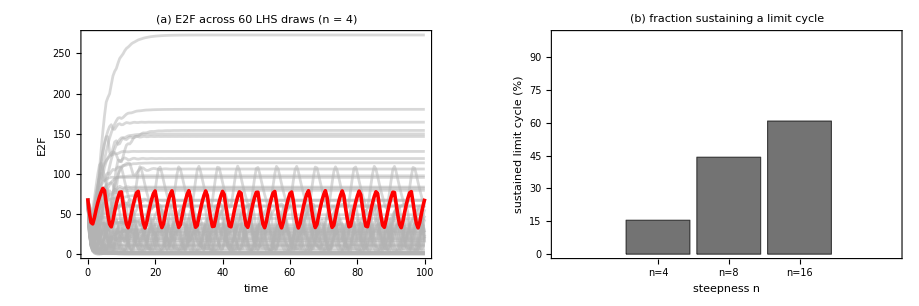

```mathematica
(* (b) fraction sustaining a limit cycle vs n, with a period histogram inset *)
fracs   = #["frac"] & /@ results;
per4    = results[[1]]["periods"];
inset   = Histogram[per4, Automatic, "Count",
   Epilog -> {Red, Thickness[0.01], Line[{{perBase, 0}, {perBase, 10^6}}]},
   Frame -> True, FrameLabel -> {"period", None},
   PlotLabel -> "period at n=4", ImageSize -> 200, LabelStyle -> 9];

panelB = BarChart[fracs,
   ChartLabels -> {"n=4", "n=8", "n=16"}, ChartStyle -> GrayLevel[0.45],
   Frame -> True, FrameLabel -> {"steepness n", "sustained limit cycle (%)"},
   PlotLabel -> "(b) fraction sustaining a limit cycle", PlotRange -> {0, 100},
   ImageSize -> 430, Epilog -> Inset[inset, Scaled[{0.30, 0.72}]]];

fig = GraphicsRow[{panelA, panelB}, Spacings -> 20, ImageSize -> 920];
Export["traynard_robustness_mma.png", fig, ImageResolution -> 130];
Print["figure written: traynard_robustness_mma.png"];
fig
```